```mathematica
data = Import["Downloads/Retention Reports - BasketballClasses.csv", "Dataset"]
```

```mathematica
labels =  Normal[data[[1]][[2;;]]];
```

```mathematica
enrolled = Normal[data[[2]][[2;;]]];
```

```mathematica
new = data[[3]][[2;;]];
```

```mathematica
returning = data[[4]][[2;;]];
```

```mathematica
MapThread[{#1, #2}&,{labels, enrolled}]
```

{{2014 Spring Basketball (Pre K - 6th),302},{2014 Fall Basketball Instructional (K - 5th),328},{14 / '15 Winter Basketball Instructional K - 5th,330},{2015 Spring Instructional Basketball PreK-5th,305},{2015-FA Instructional Basketball (Pre-K - 5th),331},{15/'16-WI Basketball Instructional (K - 5th),328},{16-SP Instructional Basketball (K-5th),262},{16-FA Basketball (K - 5th),312},{16-WI Basketball (K-5th),332},{17-SP Basketball (K-5th),307},{17-FA Basketball (K - 6th),337},{17-WI Basketball (K - 6th),332},{18-SP Basketball (K - 6th),272},{18-FA Basketball (K - 6th),260},{18-WI Basketball (K - 6th),314},{19-SP Basketball (K - 6th),271},{19-FA Basketball (K - 6th),228},{19-WI Basketball (K-6),259},{20-SP Basketball (K-6),143},{20-FA Basketball,148},{21-WI Basketball Classes (FB),144},{21-WI (2) Basketball Classes (FB),171},{21-SP Basketball Classes,150},{21-FA Basketball Classes (K - 6th),287},{22-WI Basketball Classes (K - 6th),308},{22-SP Basketball Classes (K - 6th),243},{22-FA Basketball Classes,278},{23-WI Basketball Classes,284},{23-SP Basketball Classes,216},{23-FA Basketball Classes,199},{24-WI Basketball Classes (PreK-6th),236},{24-SP Basketball Classes (Pre K - 6th),221}}

```mathematica
labelsShort = Table[{"SP", "FA", "WI"}, 10]
```

```mathematica
labelsShort = {{"14SP","14FA","15WI"},{"15SP","15FA","16WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"},{"SP","FA","WI"}}
```

```mathematica
fun=LLMExampleFunction[{"Convert the season name into its corresponding abbreviation. Seasons with two years should be converted to the later year.",{"2014 Spring Basketball (Pre K - 6th)"->"14SP","14 / '15 Winter Basketball Instructional K - 5th"->"15WI", "21-FA Basketball Classes"->"21FA"}}]
```

LLMFunction[…]

```mathematica
fun["21-WI (2) Basketball Classes (FB)"]
```

21WI

```mathematica
labelsShort = fun/@ labels
```

```mathematica
labelsShort2 = {"14SP","14FA","14WI","15SP","15FA","15WI","16SP","16FA","16WI","17SP","17FA","17WI","18SP","18FA","18WI","19SP","19FA","19WI","20SP","20FA","21WI","21WI","21SP","21FA","22WI","22SP","22FA","23WI","23SP","23FA","24WI","24SP"}
```

{14SP,14FA,14WI,15SP,15FA,15WI,16SP,16FA,16WI,17SP,17FA,17WI,18SP,18FA,18WI,19SP,19FA,19WI,20SP,20FA,21WI,21WI,21SP,21FA,22WI,22SP,22FA,23WI,23SP,23FA,24WI,24SP}

```mathematica
Column[labels]
```

2014 Spring Basketball (Pre K - 6th)
2014 Fall Basketball Instructional (K - 5th)
14 / '15 Winter Basketball Instructional K - 5th
2015 Spring Instructional Basketball PreK-5th
2015-FA Instructional Basketball (Pre-K - 5th)
15/'16-WI Basketball Instructional (K - 5th)
16-SP Instructional Basketball (K-5th)
16-FA Basketball (K - 5th)
16-WI Basketball (K-5th)
17-SP Basketball (K-5th)
17-FA Basketball (K - 6th)
17-WI Basketball (K - 6th)
18-SP Basketball (K - 6th)
18-FA Basketball (K - 6th)
18-WI Basketball (K - 6th)
19-SP Basketball (K - 6th)
19-FA Basketball (K - 6th)
19-WI Basketball (K-6)
20-SP Basketball (K-6)
20-FA Basketball
21-WI Basketball Classes (FB)
21-WI (2) Basketball Classes (FB)
21-SP Basketball Classes
21-FA Basketball Classes (K - 6th)
22-WI Basketball Classes (K - 6th)
22-SP Basketball Classes (K - 6th)
22-FA Basketball Classes
23-WI Basketball Classes
23-SP Basketball Classes
23-FA Basketball Classes
24-WI Basketball Classes (PreK-6th)
24-SP Basketball Classes (Pre K - 6th)

```mathematica
{{"2014 Spring Basketball (Pre K - 6th)"}, {"2014 Fall Basketball Instructional (K - 5th)"}, {"14 / '15 Winter Basketball Instructional K - 5th"}, {"2015 Spring Instructional Basketball PreK-5th"}, {"2015-FA Instructional Basketball (Pre-K - 5th)"}, {"15/'16-WI Basketball Instructional (K - 5th)"}, {"16-SP Instructional Basketball (K-5th)"}, {"16-FA Basketball (K - 5th)"}, {"16-WI Basketball (K-5th)"}, {"17-SP Basketball (K-5th)"}, {"17-FA Basketball (K - 6th)"}, {"17-WI Basketball (K - 6th)"}, {"18-SP Basketball (K - 6th)"}, {"18-FA Basketball (K - 6th)"}, {"18-WI Basketball (K - 6th)"}, {"19-SP Basketball (K - 6th)"}, {"19-FA Basketball (K - 6th)"}, {"19-WI Basketball (K-6)"}, {"20-SP Basketball (K-6)"}, {"20-FA Basketball"}, {"21-WI Basketball Classes (FB)"}, {"21-WI (2) Basketball Classes (FB)"}, {"21-SP Basketball Classes"}, {"21-FA Basketball Classes (K - 6th)"}, {"22-WI Basketball Classes (K - 6th)"}, {""22-Sc}, {"22-FA Basketball Classes"}, {"23-WI Basketball Classes"}, {"23-SP Basketball Classes"}, {"23-FA Basketball Classes"}, {"24-WI Basketball Classes (PreK-6th)"}, {"24-SP Basketball Classes (Pre K - 6th)"}}
```

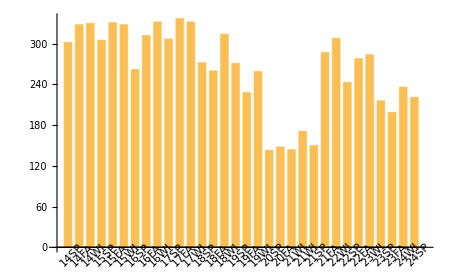

```mathematica
BarChart[enrolled, ChartLabels->Placed[labelsShort2, Below, Rotate[#, Pi/4]&]]
```

```mathematica
ListLinePlot[{enrolled, new, returning}, PlotLegends->Automatic, ]
```

-Graphics-

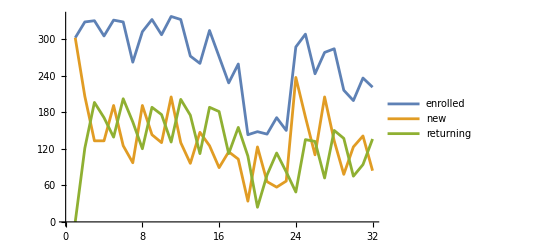

```mathematica
retention = data[[5]][[3;;]];
```

```mathematica
SemanticInterpretation[Normal[retention[[1]]]]
```

40.1 %

```mathematica
Interpreter["SemanticNumber"][Normal[retention[[1]]]]
```

Failure[…]

```mathematica
retentionN = SemanticInterpretation/@ retention
```

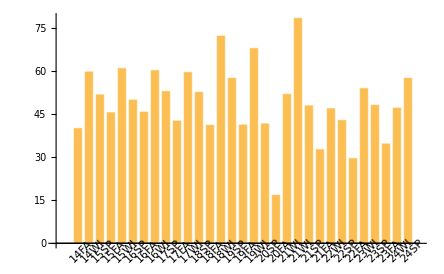

```mathematica
[retentionN, ChartLabels->Placed[labelsShort2, Below, Rotate[#, Pi/4]&]]
```